# El lenguaje Wolfram, y Mathematica: modelación en ciencias e ingeniería

## Jorge Ramirez Escuela de Matemáticas, UNALMED Facultad de Minas, UNALMED Febrero 12, 2018.

## Introducción

Bajo la iniciativa de la Dirección Académica, La Sede acaba de adquirir una licencia ilimitada de Mathematica por dos años. El objetivo es la introducción de herramientas pedagógicas modernas para la enseñanza en ciencia e ingeniería. 

Pero Mathematica permite hacer mucho más que eso:

Generación de material didáctico interactivo.

Producción de documentos técnicos integrados a cómputos científicos.

Un lenguaje de programación de altísimo nivel con ayuda interactiva.

Cálculos numéricos y simbólicos a cualquier escala.

Acceso a la base de datos computable más grande del mundo.

## El ambiente de trabajo

El cuaderno .nb

Material de clase y CDFs

Documentos técnicos.

## Aritmética y funciones

### La aritmética es exacta

Los números se pueden manejar: exactos,con precisión arbitraria, o precisión de máquina. 
Este es un cálculo exacto:

```mathematica
ⅇ^(2π)
```

```mathematica
Precision[%]
```

del cual puedo obtener cualquier precisión:

```mathematica
N[ⅇ^(2π),100]
```

O lo puedo realizar con precisión de Máquina

```mathematica
ⅇ^(2. 3.14)
```

```mathematica
Precision[%]
```

```mathematica
$MachinePrecision
```

O lo puedo hacer con la precisión que yo quiera

```mathematica
SetPrecision[ⅇ^(2. 3.14),20]
```

```mathematica
Precision[%]
```

La artimética es compleja por defecto:

```mathematica
ⅇ^(2π ⅈ)
```

### Funciones

Los argumentos que reciben las funciones pueden ser de muchos tipos

```mathematica
f[x_]:=√x;
```

```mathematica
f[({{8., x^2}, {{4,-5,6}, -Graphics-}})]
```

```mathematica
MatrixForm[%]
```

Se puede restringir los argumentos

```mathematica
fI[n_Integer]:=RandomGraph[BernoulliGraphDistribution[n,0.5]];
```

```mathematica
fI[0.5]
```

```mathematica
fI[20]
```

```mathematica
EdgeCount[]
```

Se pueden usar unidades

```mathematica
y[t_]:=-Quantity[9.8, ("Meters")/("Seconds")^2] t^2+Quantity[10, ("Meters")/("Seconds")] t+Quantity[1, "Meters"];
```

```mathematica
y[Quantity[1, "Seconds"]]
```

1.2 m

```mathematica
y'[Quantity[2, "Seconds"]]
```

-29.2 m/s

#### Funciones de funciones y funciones anónimas

Un paso del método de Newton: es una función que recibe una función f y número x0

```mathematica
newtonStep=Function[{f,x0},
x0-f[x0]/f'[x0]
];
```

Esto es una función anónima: no se especifica la variable.

```mathematica
g=(#^2+2#-3)&;
```

```mathematica
newtonStep[g,√2]
```

El método de Newton en una línea:

```mathematica
Nest[newtonStep[g,#]&,√2,2]
```

```mathematica
N[%]
```

Mathematica puede hallar esa raíz de varias formas:

```mathematica
Solve[g[x]==0,x]
```

```mathematica
NSolve[g[x]==0,x]
```

```mathematica
FindRoot[g[x],{x,√2}]
```

Una función que usa el método de Newton y devuelve un objeto interactivo:

```mathematica
newtonPlot[f_,x0_,n_]:=DynamicModule[{gl},
gl=NestList[newtonStep[f,#]&,x0,n];
Manipulate[
Plot[f[x],{x,1-ϵ,1+ϵ},
GridLines->{gl,None},PlotRange->{{1-ϵ,1+ϵ},All}
],{{ϵ,1},0.001,1}]
]
```

```mathematica
newtonPlot[g,√2,3]
```

## Visualización

Funciones de una variable

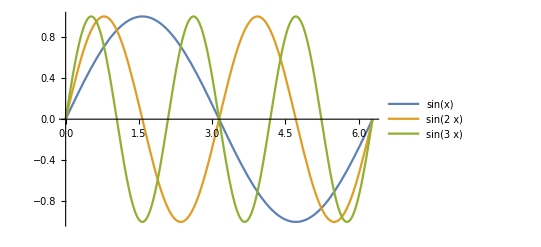

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotLegends->"Expressions"]
```

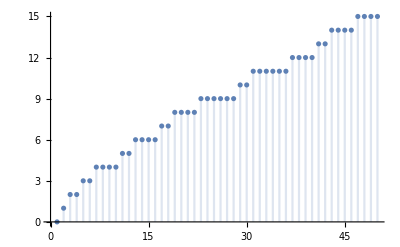

```mathematica
DiscretePlot[PrimePi[n],{n,50},PlotMarkers->Point,AxesOrigin->{0,0}]
```

Regiones dadas por desigualdades

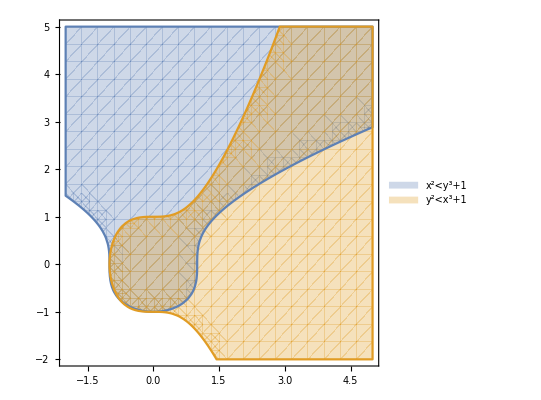

```mathematica
RegionPlot[{x^2<y^3+1,y^2<x^3+1},{x,-2,5},{y,-2,5},PlotLegends->"Expressions"]
```

Curvas y regiones paramétricas

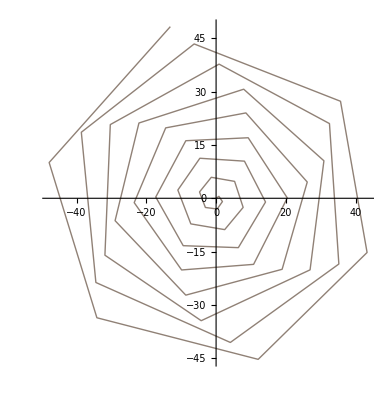

```mathematica
ParametricPlot[{Sin[u]u ,Cos[u]u}, 
{u,0,50},PlotPoints->50,Axes->True,ColorFunction->(ColorData["Rainbow"][#3]&),MaxRecursion->0,PlotStyle->Thick]
```

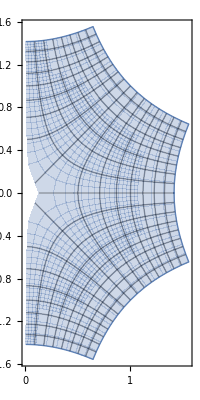

```mathematica
ParametricPlot[{Re[(u+ⅈ v)^(1/2)],Im[(u+ⅈ v)^(1/2)]},{u,-2,2},{v,-2,2},Mesh->Automatic]
```

Campos vectoriales y líneas de flujo

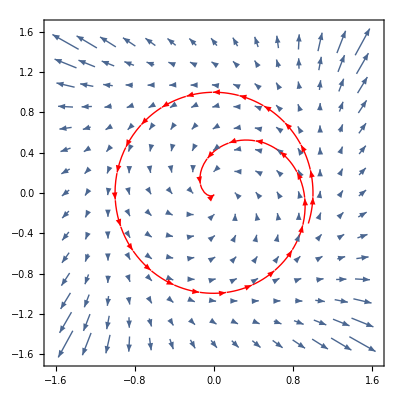

```mathematica
VectorPlot[ {α x-y-α x(x^2+y^2), x+α y-α y(x^2+y^2)}/.α->-1,{x,-1.5,1.5},{y,-1.5,1.5},StreamPoints->{{{0.5,0.5}}},StreamStyle->Red]
```

Funciones de dos variables

```mathematica
Plot3D[Im[ArcSin[(x+ⅈ y)^4]],{x,-2,2},{y,-2,2},Mesh->Automatic,ExclusionsStyle->{None,Red}]
```

-Graphics3D-

```mathematica
Plot3D[Abs@ArcCot[x+ⅈ y],{x,-2,2},{y,-2,2},MeshFunctions->Function@@@{{{x,y,z},Re[ArcCot[x+ⅈ y]]},{{x,y,z},Im[ArcCot[x+ⅈ y]]}},MeshStyle->{Blue,Red},PlotLabel->ArcCot,ImageSize->Medium]
```

-Graphics3D-

Superficies paramétricas

```mathematica
ParametricPlot3D[{{4+(3+Cos[v]) Sin[u],4+(3+Cos[v]) Cos[u],4+Sin[v]},{8+(3+Cos[v]) Cos[u],3+Sin[v],4+(3+Cos[v]) Sin[u]}},{u,0,2Pi},{v,0,2Pi},PlotStyle->{Red,Green}]
```

-Graphics3D-

Superficies de nivel

```mathematica
ContourPlot3D[ Cos[x]Sin[y]+Cos[y]Sin[z]+Cos[z]Sin[x]==0,{x,-2π,2π}, {y,-2π,2π},{z,-2π,2π},ContourStyle->Directive[FaceForm[Orange,Red],Specularity[White,30]],Mesh->None]
```

-Graphics3D-

Una función de tres variables en la bola unitaria

```mathematica
DensityPlot3D[Sin[x]Cos[y]Sin[z],{x,y,z}∈Ball[{0,0,0},5]]
```

-Graphics3D-

Todos los poliedros

```mathematica
PolyhedronData[{"PentagonalHexecontahedron","Laevo"}]
```

-Graphics3D-

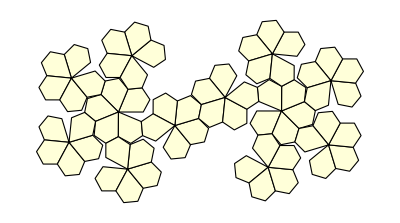

```mathematica
PolyhedronData[{"PentagonalHexecontahedron","Laevo"},"Net"]
```

Hay una libreria de fractales

```mathematica
MandelbrotSetPlot[{-0.65+0.47ⅈ,-0.4+0.72ⅈ},PlotLegends->Automatic]
```

-Graphics-

Mapas de elevación

```mathematica
mde=GeoBoundsRegion[Entity["City",{"Medellin","Antioquia","Colombia"}],LinguisticAssistant];
ReliefPlot[Reverse@GeoElevationData[mde],PlotLegends->Automatic]
```

-Graphics-

```mathematica
Exit[];
```

## Expresiones simbólicas

### Manipulación

```mathematica
e1=((-1+x)^2 (2+x))/((-3+x)^2 (1+x));
```

```mathematica
Expand[e1]
```

2/((-3+x)^2 (1+x))-(3 x)/((-3+x)^2 (1+x))+x^3/((-3+x)^2 (1+x))

```mathematica
ExpandAll[e1]
```

2/(9+3 x-5 x^2+x^3)-(3 x)/(9+3 x-5 x^2+x^3)+x^3/(9+3 x-5 x^2+x^3)

```mathematica
Together[%]
```

(2-3 x+x^3)/((-3+x)^2 (1+x))

```mathematica
Factor[%]
```

((-1+x)^2 (2+x))/((-3+x)^2 (1+x))

```mathematica
e2=9 x^2+12 x^3+4 x^4+36 x y+48 x^2 y+16 x^3 y+36 y^2+48 x y^2+16 x^2 y^2;
```

```mathematica
Collect[e2,x]
```

4 x^4+36 y^2+x^3 (12+16 y)+x^2 (9+48 y+16 y^2)+x (36 y+48 y^2)

```mathematica
Collect[e2,y]
```

9 x^2+12 x^3+4 x^4+(36 x+48 x^2+16 x^3) y+(36+48 x+16 x^2) y^2

```mathematica
Factor[e2]
```

(3+2 x)^2 (x+2 y)^2

```mathematica
Factor[x^10-1,Modulus->3]
```

(1+x) (2+x) (1+x+x^2+x^3+x^4) (1+2 x+x^2+2 x^3+x^4)

### Simplificación

Las simplificaciones se pueden hacer con suposiciones:

```mathematica
Sin[n π]
```

```mathematica
Simplify[Sin[n π],n∈Integers]
```

```mathematica
Assuming[p∈Reals∧x>0,
Simplify[Log[x^p]]
]
```

O de hecho, cualquier cálculo

```mathematica
Assuming[n<1,∫_0^1 1/x^n ⅆx]
```

```mathematica
Assuming[n>2,∫_0^1 1/x^n ⅆx]
```

```mathematica
Exit[]
```

### En los complejos

Simplificaciones en los complejos suponiendo que x, y son reales

```mathematica
ComplexExpand[Re[Sin[x+ⅈ y]]]
```

Cosh[y] Sin[x]

Expanda una expresión suponiendo que x es compleja

```mathematica
ComplexExpand[Sin[x],x]
```

Cosh[Im[x]] Sin[Re[x]]+ⅈ Cos[Re[x]] Sinh[Im[x]]

Convertir a exponenciales

```mathematica
TrigToExp[Cos[x]]
```

ⅇ^(-ⅈ x)/2+ⅇ^(ⅈ x)/2

```mathematica
DSolve[{y''[t]+ω^2 y[t]==0,y[0]==1,y'[0]==I ω},y[t],t]
```

{{y[t]→Cos[t ω]+ⅈ Sin[t ω]}}

```mathematica
TrigToExp[%]
```

{{y[t]→ⅇ^(ⅈ t ω)}}

Tomemos una función analítica y escribámosla en términos de las partes real e imaginaria de z para mostrar que satisface la ecuación de Laplace

```mathematica
f[z_]:=z^2 Sin[z+z^3]+Tan[1/z];
ComplexExpand[f[x+ⅈ y]]
```

Sin[(2 x)/(x^2+y^2)]/(Cos[(2 x)/(x^2+y^2)]+Cosh[(2 y)/(x^2+y^2)])+x^2 Cosh[y+3 x^2 y-y^3] Sin[x+x^3-3 x y^2]-y^2 Cosh[y+3 x^2 y-y^3] Sin[x+x^3-3 x y^2]-2 x y Cos[x+x^3-3 x y^2] Sinh[y+3 x^2 y-y^3]+ⅈ (2 x y Cosh[y+3 x^2 y-y^3] Sin[x+x^3-3 x y^2]-Sinh[(2 y)/(x^2+y^2)]/(Cos[(2 x)/(x^2+y^2)]+Cosh[(2 y)/(x^2+y^2)])+x^2 Cos[x+x^3-3 x y^2] Sinh[y+3 x^2 y-y^3]-y^2 Cos[x+x^3-3 x y^2] Sinh[y+3 x^2 y-y^3])

```mathematica
FullSimplify[∂_(x,x) %+∂_(y,y) %]
```

0

### Integrales

Una integral indefinida, y su derivada:

```mathematica
∫1/(x^3+1)ⅆx
```

```mathematica
D[%,x]
```

```mathematica
Simplify[%]
```

```mathematica
∫_(-∞)^∞ Exp[-c x^2]ⅆx
```

ConditionalExpression[(√π)/(√c),Re[c]>0]

Integral doble simbólica

```mathematica
∫_0^1 ∫_0^z Sin[x y]ⅆyⅆx
```

EulerGamma-CosIntegral[z]+Log[z]

Integral con función indefinida

```mathematica
Integrate[f''[x]+2 a f'[x],x]
```

2 a f[x]+f'[x]

Integral sobre regiones

```mathematica
Integrate[Boole[x^2+y^2<a],{x,0,1},{y,0,1}]
```

Piecewise[{{1, a≥2}, {(a π)/4, 0<a≤1}, {1/2 (2 √(-1+a)+a ArcCsc[√a]-a ArcTan[√(-1+a)]), 1<a<2}, {0, True}}]

Integrales de superficie, volumen,...

```mathematica
Integrate[x^3 y^3+z^4,{x,y,z}∈Tetrahedron[{{0,0,0},{1,0,0},{0,1,0},{0,0,1}}]]
```

7/1440

```mathematica
Integrate[1,{x,y,z}∈Sphere[{0,0,0},r]]
```

ConditionalExpression[4 π r^2,r>0]

```mathematica
Integrate[1,{x,y,z}∈Ball[{0,0,0},r]]
```

ConditionalExpression[(4 π r^3)/3,r>0]

Integral de contorno en ℂ

```mathematica
Integrate[1/(z(z-3ⅈ)),{z,1-ⅈ,1+ⅈ,-1+ⅈ,-1-ⅈ,1-ⅈ}]
```

1/6 (-π+ArcTan[240/161])+1/6 (-2 π+ArcTan[24/7])+1/6 (-π+ArcTan[36/77]-ⅈ Log[17/5])+1/6 (-π+ArcTan[36/77]+ⅈ Log[17/5])

```mathematica
FullSimplify[%]
```

-(2 π)/3

```mathematica
Residue[1/(z(z-3ⅈ)),{z,0}]
```

ⅈ/3

### Expansiones y Transformadas

Series de potencia

```mathematica
Series[Sin[x],{x,0,10}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11

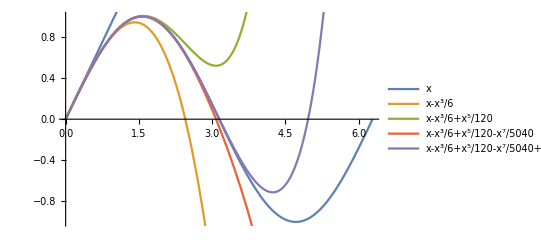

```mathematica
Show[
Plot[Sin[x],{x,0,2π}],
Plot[Evaluate[Table[Normal[Series[Sin[x],{x,0,n}]],{n,1,10,2}]],{x,0,2π},PlotLegends->"Expressions"]
]
```

Dada una función generatriz

```mathematica
gf=1/Apply[Times,1-z^{1,5,10,25,50,100}]
```

1/((1-z) (1-z^5) (1-z^10) (1-z^25) (1-z^50) (1-z^100))

```mathematica
SeriesCoefficient[Series[gf,{z,0,100}],100]
```

293

Series de Fourier

```mathematica
FourierSeries[Abs[t],t,2]
```

-(2 ⅇ^(-ⅈ t))/π-(2 ⅇ^(ⅈ t))/π+π/2

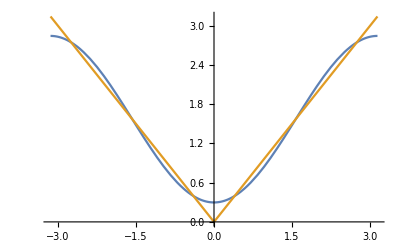

```mathematica
Plot[{%, Abs[t]}, {t,-π, π}]
```

Otras transformadas

```mathematica
Names["System`*Transform"]
```

{AffineTransform,BottomHatTransform,ConfidenceTransform,ContinuousWaveletTransform,CoordinateTransform,DirichletTransform,DiscreteChirpZTransform,DiscreteHadamardTransform,DiscreteWaveletPacketTransform,DiscreteWaveletTransform,DistanceTransform,FillingTransform,FindGeometricTransform,FourierCosTransform,FourierSequenceTransform,FourierSinTransform,FourierTransform,HankelTransform,HistogramTransform,HitMissTransform,InverseContinuousWaveletTransform,InverseDistanceTransform,InverseFourierCosTransform,InverseFourierSequenceTransform,InverseFourierSinTransform,InverseFourierTransform,InverseHankelTransform,InverseLaplaceTransform,InverseMellinTransform,InverseWaveletTransform,InverseZTransform,LaplaceTransform,LiftingWaveletTransform,LinearFractionalTransform,ListFourierSequenceTransform,ListZTransform,MellinTransform,MorphologicalTransform,ReflectionTransform,RescalingTransform,RotationTransform,ScalingTransform,ShearingTransform,SkeletonTransform,StateSpaceTransform,StationaryWaveletPacketTransform,StationaryWaveletTransform,TopHatTransform,TransferFunctionTransform,TranslationTransform,ZTransform}

```mathematica
FourierTransform[HeavisideTheta[t],t,ω]
```

ⅈ/(√(2 π) ω)+√(π/2) DiracDelta[ω]

```mathematica
Clear[f];
∫_(-∞)^∞ DiracDelta[x]f[x]ⅆx
```

f[0]

```mathematica
LaplaceTransform[f''[t],t,s]
```

-s f[0]+s^2 LaplaceTransform[f[t],t,s]-f'[0]

## Geometría

Regiones a partir de expresiones implicitas

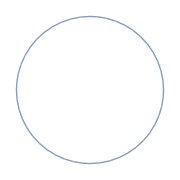

```mathematica
Region[
ImplicitRegion[x^2+y^2==1,{x,y}],
ImageSize->Small]
```

```mathematica
Region[
ImplicitRegion[-4 y^2-4 x y^2+y^4+4 x z^2+4 x^2 z^2+2 y^2 z^2+z^4==0,{x,y,z}],
ImageSize->Small
]
```

-Graphics3D-

```mathematica
Region[
ImplicitRegion[x^2+y^2+z^2<1||(x+1)^2+y^2+z^2<1,{x,y,z}],
ImageSize->Small]
```

-Graphics3D-

Regiones a partir de listas

```mathematica
Region[
DelaunayMesh[RandomReal[1,{50,3}]],
ImageSize->Small
]
```

-Graphics3D-

Regiones parametrizadas y con restricciones

```mathematica
Region[
ParametricRegion[{{x,y,z+y x},
x^2+y^2+z^2≤1 || z==Sin[x+y]},
{{x,-1,1},{y,-1,1},{z,-2,2}}],
ImageSize->Small]
```

-Graphics3D-

Operaciones y transformaciones de regiones

```mathematica
r1=Triangle[];
r2=Disk[{1/2,1/2},1/4];
```

```mathematica
RegionMeasure[r1]
```

1/2

```mathematica
RegionDistance[r2,{6,5}]
```

-1/2+√(101/2)

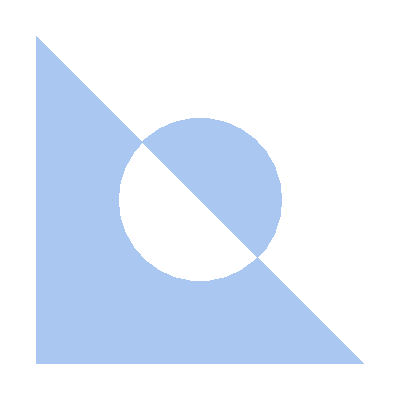

```mathematica
Region[
RegionSymmetricDifference[r1,r2]
]
```

## Ecuaciones: Solve y DSolve

### Ecuaciones algebraicas

```mathematica
Solve[(x^4-1)(x^4-4)==0,x]
```

Se puede especificar el dominio donde se resuelve:

```mathematica
Solve[(x^4-1)(x^4-4)==0,x,Reals]
```

```mathematica
Solve[(x^4-1)(x^4-4)==0,x,Integers]
```

Hay ecuaciones que tienen muchas soluciones:

```mathematica
Solve[Sin[x]==1/3,x]
```

Ecuaciones geométricas

```mathematica
ptsHC=Solve[{x,y}∈InfiniteLine[{{0,0},{2,1}}]∧{x,y}∈HilbertCurve[4],{x,y}]
```

{{x→0,y→0},{x→1,y→1/2},{x→2,y→1},{x→3,y→3/2},{x→4,y→2},{x→5,y→5/2},{x→6,y→3},{x→8,y→4},{x→10,y→5},{x→12,y→6},{x→13,y→13/2},{x→14,y→7},{x→15,y→15/2}}

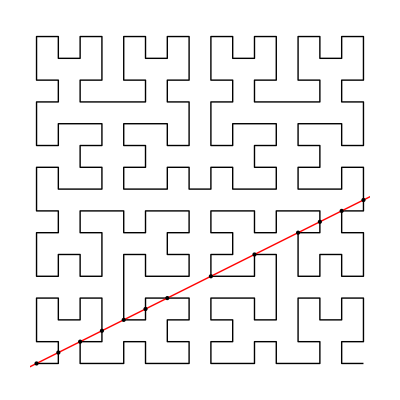

```mathematica
Graphics[{
{Red,Thick,InfiniteLine[{{0,0},{2,1}}]},
HilbertCurve[4],
{PointSize[Large],Point[{x,y}/.ptsHC]}
}]
```

### Ecuaciones Diferenciales Ordinarias

Una ecuación sin condiciones iniciales. La solución tiene constantes libres

```mathematica
sol1=DSolve[y'[x]+y[x]==a Sin[x],y[x],x]⟦1,1⟧
```

Grafiquemos varios miembros de la familia de soluciones dándole valores a C[1]

```mathematica
Plot[
Evaluate@Table[
(y[x]/.sol1)/.{a->0.5,C[1]->c},
{c,{1,2,3}}],
{x,0,5},PlotLegends->"Expressions"]
```

Una problema de valor inicial con condición de frontera simbólica:

```mathematica
DSolve[{y'[x]+y[x]==a Sin[x],y[0]==b},y[x],x]⟦1,1⟧
```

Una problema de valor inicial con coeficientes discontinuos :

```mathematica
DSolve[{y'[x]+y[x]==a UnitBox[x],y[0]==b},y[x],x]⟦1,1⟧
```

#### Un sistema dinámico en 2D:

```mathematica
solSD[{x0_,y0_}]=DSolve[{
{x'[t],y'[t]}==({{-1/10, 1}, {-1, -1/2}}).{x[t],y[t]},
{x[0],y[0]}=={x0,y0}
},
{x[t],y[t]},t]⟦1⟧
```

```mathematica
Manipulate[
ParametricPlot[({x[t],y[t]}/.solSD[p]),{t,0,20},PlotRange->2],{{p,{1,1}},{-2,-2},{2,2}},ControlType->Locator,SaveDefinitions->True
]
```

### Ecuaciones Diferenciales Parciales

La ecuación de calor con condiciones de Neumann

```mathematica
DSolve[{
D[u[x,t], t]==D[u[x,t], x,x],
u[x,0]==DiracDelta[x-3],
Derivative[1,0][u][0, t] ==0},
u[x,t],{x,t}]
```

{{u[x,t]→Piecewise[{{(ⅇ^(-(-3+x)^2/(4 t))+ⅇ^(-(3+x)^2/(4 t)))/(2 √π √t), x>0}, {Indeterminate, True}}]}}

La ecuación KdV

```mathematica
solKdV= DSolve[
{D[u[x,t],t]+D[u[x,t],{x, 3}]+ 6u[x,t]D[u[x,t],x]==0},
u[x,t],{x,t}]
```

DSolve::nlpde: Solution requested to nonlinear partial differential equation. Trying to build a special solution.

{{u[x,t]→-(-8 C[1]^3+C[2]+12 C[1]^3 Tanh[x C[1]+t C[2]+C[3]]^2)/(6 C[1])}}

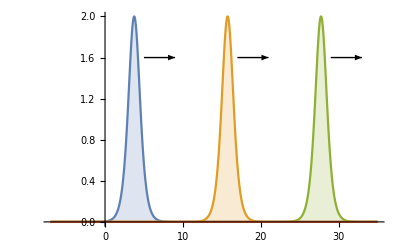

```mathematica
Plot[Evaluate[Table[
(u[x,t]/.solKdV)/.{C[1]->1,C[2]->-4,C[3]->1/4}
,{t,1,12,3}]], {x,-7,35},PlotRange->All,Filling->Axis,Epilog->{Arrow[{{5,1.6},{9,1.6}}],Arrow[{{17,1.6},{21,1.6}}],Arrow[{{29,1.6},{33,1.6}}]}]
```

Ecuación de Laplace en un disco

```mathematica
solLap=DSolve[{
u[x,y]{x,y}==0,
 DirichletCondition[u[x, y]==Sin[6ArcTan[y/x]], True]
 },u[x,y],{x,y}∈Disk[{0,0},3]]
```

{{u[x,y]→1/729 (x^2+y^2)^3 Sin[6 ArcTan[y/x]]}}

```mathematica
Plot3D[u[x,y]/.solLap⟦1⟧//Evaluate,{x,y}∈Disk[{0,0},3],PlotRange->All,PlotStyle->Hue[0.5]]
```

-Graphics3D-

La ecuación de Bessel para u(r,t):

```mathematica
sol=u[r,t]/.DSolve[{
r D[u[r,t],t]==D[r D[u[r,t],r],r],(*EDP*)
u[r,0]==1-r,(*cond. inicial*)
u[1,t]==0 (*cond. de frontera*)
},u[r,t],{r,t}]⟦1⟧;
```

La solución es una serie infinita e involucra funciones especiales

```mathematica
sol//TraditionalForm
```

Saquemos los primeros tres términos de la suma y evaluemos numéricamente los coeficientes:

```mathematica
h[r_,t_]=sol/.{∞->3}//Activate//N
```

Grafiquemos los tres primeras funciones (propias) de la suma y en función de (x,y):

```mathematica
Table[
Plot3D[
Evaluate[h[r,0.1]⟦i⟧/.{r->√(x^2+y^2)}],
{x,y}∈Disk[],Ticks->None],
{i,3}]
```

```mathematica
Exit[]
```

## Cálculos Numéricos

### Integración numérica

Hay integrales que no tienen expresión cerrada

```mathematica
Integrate[BesselJ[0,x]/(1+x),{x,0,1}]
```

```mathematica
NIntegrate[BesselJ[0,x]/(1+x),{x,0,1}]
```

Las integrales númericas se pueden hacer sobre cualquier dominio. 
Este es un modelo del casco del HydroFoil:

```mathematica
SetDirectory[NotebookDirectory[]];
hull=Import["Casco.STL","BoundaryMeshRegion"];
Show[hull,Axes->True,ImageSize->300]
```

Integremos la función f(x,y,z)=z dentro del sólido

```mathematica
NIntegrate[z,{x,y,z}∈hull]
```

### Optimización y cálculos en paralelo

Supongamos que queremos hallar los mínimos locales de esta función

```mathematica
h[x_]:=Cos[x]Sin[4x]Exp[-0.01x];
Plot[h[x],{x,0,30}]
```

La función FindMinimum[f,x0] lo hace empezando desde el punto x0. Devuelve  {f(x_min),x_min}

```mathematica
FindMinimum[h[x],{x,10}]
```

Creamos una colección de valores de x en el dominio

```mathematica
xs=Range[0,30,0.5]
```

y evaluamos la función FindMinimum[h[x],#]& en cada uno de los xs

```mathematica
mins=Quiet@FindMinimum[h[x],{x,#}]&/@xs;
```

Grafiquemos la función h y los puntos que obtuvimos

```mathematica
Show[
Plot[h[x],{x,0,30}],
ListPlot[{x/.mins⟦All,2⟧,mins⟦All,1⟧}ᵀ,PlotStyle->Red,PlotMarkers->{Automatic,8}]
]
```

Las evaluaciones de FindMinimum empezando en cada x0 no dependen una de la otra. Entonces podemos hacer ese cálculo en paralelo, en vez de en serie. La función Parallelize evalua cualquier expresión en kernels locales paralelos de manera automática.
El resultado es el mismo:

```mathematica
minsp=Parallelize[
Quiet@FindMinimum[h[x],{x,#}]&/@xs
];
Show[
Plot[h[x],{x,0,30}],
ListPlot[{x/.minsp⟦All,2⟧,minsp⟦All,1⟧}ᵀ,PlotStyle->Green,PlotMarkers->{Automatic,8}]
]
```

Pero usemos Timing para comparar los tiempos de ejecución (en segundos):

```mathematica
Timing[Quiet@FindMinimum[h[x],{x,#}]&/@xs]⟦1⟧
```

```mathematica
Timing[Parallelize[
Quiet@FindMinimum[h[x],{x,#}]&/@xs
]]⟦1⟧
```

### Funciones de interpolación

Definamos una función interpolada a partir de una tabla de datos en 3D

```mathematica
lcm=Flatten[Table[{{x,y},LCM[x,y]},{x,4},{y,4}],1]
```

{{{1,1},1},{{1,2},2},{{1,3},3},{{1,4},4},{{2,1},2},{{2,2},2},{{2,3},6},{{2,4},4},{{3,1},3},{{3,2},6},{{3,3},3},{{3,4},12},{{4,1},4},{{4,2},4},{{4,3},12},{{4,4},4}}

```mathematica
fInt=Interpolation[lcm]
```

InterpolatingFunction[{{1, 4}, {1, 4}}, <>]

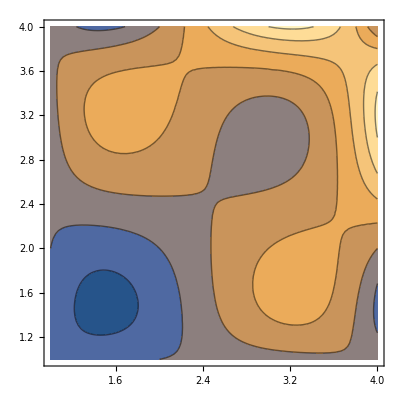

```mathematica
ContourPlot[fInt[x,y],{x,1,4},{y,1,4}]
```

La derivada de fInt es otra función de interpolación

```mathematica
D[fInt[x,y],x]
```

InterpolatingFunction[{{1, 4}, {1, 4}}, <>][x,y]

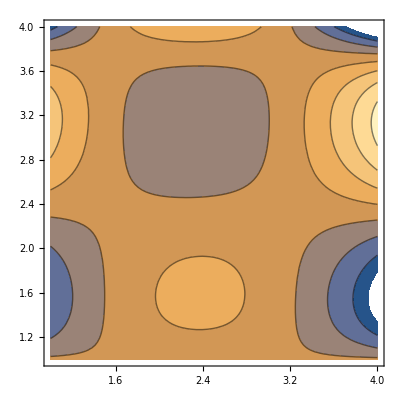

```mathematica
ContourPlot[%,{x,1,4},{y,1,4}]
```

Splines

```mathematica
pts={{1,1},{2,3},{3,-1},{4,1},{5,0}};
fSp=BSplineFunction[pts]
```

BSplineFunction[{{0., 1.}}, <>]

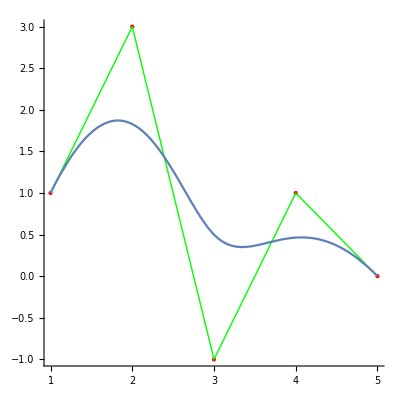

```mathematica
Show[Graphics[{Red,Point[pts],Green,Line[pts]},Axes->True],ParametricPlot[fSp[t],{t,0,1}]]
```

Un parche Bezier

```mathematica
pts={{{0,0,0},{0,1,0},{0,2,0},{0,3,0}},{{1,0,0},{1,1,1},{1,2,1},{1,3,0}},
{{2,0,0},{2,1,1},{2,2,1},{2,3,0}},
{{3,0,0},{3,1,0},{3,2,0},{3,3,0}}};
fBez=BezierFunction[pts]
```

BezierFunction[{{0., 1.}, {0., 1.}}, <>]

```mathematica
Show[Graphics3D[{PointSize[Medium],Red,Map[Point,pts]}],
Graphics3D[{Gray,Line[pts],Line[Transpose[pts]]}],ParametricPlot3D[fBez[u,v],{u,0,1},{v,0,1},Mesh->Automatic]]
```

-Graphics3D-

## Ecuaciones: NSolve y NDSolve

### Solución numérica a ecuaciones

#### Ecuaciones, desigualdades y dominios

```mathematica
NSolve[{Sin[x+y]==1/2,
ⅇ^x-y==1,
x^2≤2},{x,y},Reals]
```

Se puede, por ejemplo, resolver problemas de existencia:

```mathematica
NSolve[
Exists[x, (x^2+a x+b==0)∧(2x+a==0)∧(a^2+x b^2==1)],
{a,b},Reals]
```

#### Ecuaciones diferenciales ordinarias

Generemos una onda con 32 componentes sinusoidales:

```mathematica
ste=0.012;
tb=25;
xb=12;
fc=0.89;
g=9.81;
h0=1.;
k0=1.2;
maxt=50;
nk=32;
k[f_]:=(2π f)^2/g;
ω[k_]:=√(g k Tanh[k h0])
ks=Table[k0 + i (k[fc]-k[fc - (0.75 fc)/2])/(nk/2),{i,0,nk-1}];
ωs=ω[ks];
as=ste/ks;
```

```mathematica
as Cos[ks(x-xb)-ωs(t-tb)]
```

Esta es la superficie

```mathematica
η[x_,t_]:=Total[as Cos[ks(x-xb)-ωs(t-tb)]];
Manipulate[
Plot[η[x,t],{x,0,25},PlotRange->{Automatic,{-0.1,0.1}},Filling->Bottom],
{t,0,maxt}]
```

Este es el potencial

```mathematica
φ[{x_,z_},t_]=Total[-(as ωs)/ks Cosh[ks(h0+z)]/Cosh[ks h0] Cos[ks (x-xb)-(t-tb) ωs]];
```

Y los campos de velocidad

```mathematica
u[{x_,z_},t_]=D[φ[{x,z},t],x];
w[{x_,z_},t_]=D[φ[{x,z},t],z];
```

Una función que resuelve la EDO del movimiento para cada posición inicial:

```mathematica
path[{x0_,z0_}]:=NDSolve[{
x'[t]==u[{x[t],z[t]},t],
z'[t]==w[{x[t],z[t]},t],
x[0]==x0,z[0]==z0},{x,z},{t,0,maxt}];
```

Cada solución es una función interpolada

```mathematica
path[{12,-0.1}]
```

que por ejemplo se puede derivar

```mathematica
lagu=D[x[t]/.path[{12,-0.1}]⟦1⟧,t]
```

```mathematica
Plot[lagu,{t,0,maxt},PlotRange->All]
```

El resultado final

```mathematica
DynamicModule[{x0=12.5,z0=-0.15,tray,plot},
tray=Evaluate[{x[t],z[t]}/.path[{x0,z0}]];
Manipulate[
Show[
Plot[η[x,tt],{x,0,25},PlotRange->{Automatic,{-0.1,0.1}},Filling->-2],
ParametricPlot[tray,{t,0,tt},PlotStyle->Red],
PlotRange->{{x0-0.5,x0+0.5},{z0-0.1,0.2}},AxesOrigin->{Automatic,0}
],
{{tt,20},1,maxt,Appearance->"Labeled"}]]
```

```mathematica
Exit[]
```

### Ecuaciones Diferenciales Parciales sobre regiones

Resolvamos la ecuación de Stokes para flujo dentro de un canal de sección variable. Primero definimos la región

```mathematica
Ω=RegionUnion[Rectangle[{0,0},{1,0.5}],Rectangle[{1,0.1},{2,0.4}]];
Show[Region[Ω],Axes->True,GridLines->Automatic]
```

Este es el sistema de EDP. Es vectorial en las variables xVel, yVel, p y tiene condiciones de frontera de Dirichlet.

```mathematica
{xVel,yVel}={u,v}/.NDSolve[{
{({{-μ,0},{0,-μ}}.u[x,y]{x,y}Inactive){x,y}Inactive+Derivative[1,0][p][x,y],({{-μ,0},{0,-μ}}.v[x,y]{x,y}Inactive){x,y}Inactive+Derivative[0,1][p][x,y],
Derivative[1,0][u][x,y]+Derivative[0,1][v][x,y]}=={0,0,0}/.μ->1,
{DirichletCondition[u[x,y]==7.13 (0.5-y) y,x==0.],DirichletCondition[{u[x,y]==0.,v[x,y]==0.},0<x<2],
DirichletCondition[p[x,y]==0.,x== 2]}
},{u,v,p},{x,y}∈Ω,Method->{"FiniteElement","InterpolationOrder"->{u->2,v->2,p->1},"MeshOptions"->{"MaxCellMeasure"->0.0005}}]⟦1⟧;
```

```mathematica
Manipulate[
Show[
Region[Ω,Frame->True],
VectorPlot[{xVel[x,y], yVel[x,y]},{x,y}∈Ω, AspectRatio->Automatic,StreamColorFunctionScaling->False,VectorStyle->Black,VectorPoints->15(1-s),StreamPoints->20 s,StreamScale->Full,StreamStyle->Black],
ImageSize->450
],{{s,0},{0,1},ControlType->Checkbox}]
```

### Regiones arbitrarias

```mathematica
mde=GeoBoundsRegion[Here,LinguisticAssistant];
```

```mathematica
p1=GeoDestination[Here,{LinguisticAssistant,-30}];
dists=Range[100,10.1^4,10^2];
ps=GeoDestination[p1,GeoDisplacement[{dists,105}]];
Show[
GeoGraphics[mde],
GeoListPlot[ps]
]
```

```mathematica
ReliefPlot[Reverse@GeoElevationData[mde],PlotLegends->Automatic]
```

```mathematica
elev=QuantityMagnitude@GeoElevationData[ps];
meshps=Join[
{dists,QuantityMagnitude@GeoElevationData[ps]}ᵀ,
{{dists⟦-1⟧,elev⟦-1⟧+100},{dists⟦1⟧,elev⟦-1⟧+100}}
];
reg=BoundaryMeshRegion[
meshps,
Line[Append[Range[1,Length[meshps]],1]]];
```

```mathematica
Show[
ListPlot[{dists,GeoElevationData[ps]}ᵀ],
reg
]
```

```mathematica
sol=u/.First[NDSolve[{
D[u[t,x,y],{t,2}]-500^2 Laplacian[u[t,x,y],{x,y}]==0,DirichletCondition[u[t,x,y]==0,True],u[0,x,y]==2Exp[-10^-5((x-5500)^2+(y-1600)^2)],Derivative[1,0,0][u][0,x,y]==0},u,{t,0,6},{x,y}∈reg]]
```

```mathematica
ListAnimate[Table[
DensityPlot[sol[t,x,y],{x,y}∈reg,AspectRatio->1,PlotRange->{Automatic,Automatic,{-0.4,12}},PlotLegends->BarLegend[{Automatic,{-0.4,12}}]],
{t,0,6,0.1}],
AnimationRepetitions->1,AnimationRunning->False]
```

## Álgebra lineal

```mathematica
m={{2,0,1},{0,1,-1},{0,1,1}};
```

```mathematica
m//MatrixForm
```

(2 | 0 | 1
0 | 1 | -1
0 | 1 | 1)

```mathematica
MatrixRank[m]
```

3

```mathematica
Inverse[m]
```

{{1/2,1/4,-1/4},{0,1/2,1/2},{0,-1/2,1/2}}

```mathematica
Eigenvalues[m]
```

{2,1+ⅈ,1-ⅈ}

```mathematica
MatrixExp[m]
```

{{ⅇ^2,ⅇ^2/2-1/2 ⅇ Cos[1]-1/2 ⅇ Sin[1],ⅇ^2/2-1/2 ⅇ Cos[1]+1/2 ⅇ Sin[1]},{0,ⅇ Cos[1],-ⅇ Sin[1]},{0,ⅇ Sin[1],ⅇ Cos[1]}}

```mathematica
MatrixForm/@JordanDecomposition[m]
```

{(-1+ⅈ | -1-ⅈ | 1
-2 ⅈ | 2 ⅈ | 0
2 | 2 | 0),(1-ⅈ | 0 | 0
0 | 1+ⅈ | 0
0 | 0 | 2)}

```mathematica
NullSpace[{{2,0,1},{0,1,-1},{0,0,0}}]
```

{{-1,2,2}}

Matrices escasas

```mathematica
s=SparseArray[{{i_,i_}->-2,{i_,j_}/;Abs[i-j]==1->1},{5,5}]
```

SparseArray[<13>, {5, 5}]

```mathematica
MatrixForm[s]
```

(-2 | 1 | 0 | 0 | 0
1 | -2 | 1 | 0 | 0
0 | 1 | -2 | 1 | 0
0 | 0 | 1 | -2 | 1
0 | 0 | 0 | 1 | -2)

## Teoría de números, álgebra

Alugnas funciones de teoría de números

```mathematica
Prime[1000]
```

7919

```mathematica
FactorInteger[2434500]
```

{{2,2},{3,2},{5,3},{541,1}}

```mathematica
Divisors[1729]
```

{1,7,13,19,91,133,247,1729}

```mathematica
IntegerPartitions[10]
```

{{10},{9,1},{8,2},{8,1,1},{7,3},{7,2,1},{7,1,1,1},{6,4},{6,3,1},{6,2,2},{6,2,1,1},{6,1,1,1,1},{5,5},{5,4,1},{5,3,2},{5,3,1,1},{5,2,2,1},{5,2,1,1,1},{5,1,1,1,1,1},{4,4,2},{4,4,1,1},{4,3,3},{4,3,2,1},{4,3,1,1,1},{4,2,2,2},{4,2,2,1,1},{4,2,1,1,1,1},{4,1,1,1,1,1,1},{3,3,3,1},{3,3,2,2},{3,3,2,1,1},{3,3,1,1,1,1},{3,2,2,2,1},{3,2,2,1,1,1},{3,2,1,1,1,1,1},{3,1,1,1,1,1,1,1},{2,2,2,2,2},{2,2,2,2,1,1},{2,2,2,1,1,1,1},{2,2,1,1,1,1,1,1},{2,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1}}

El pequeño teorema de Fermat

```mathematica
Simplify[Mod[a^p,p],a∈Integers ∧ p ∈Primes]
```

Mod[a,p]

Grupos

```mathematica
SymmetricGroup[4]//GroupElements
```

{Cycles[{}],Cycles[{{3,4}}],Cycles[{{2,3}}],Cycles[{{2,3,4}}],Cycles[{{2,4,3}}],Cycles[{{2,4}}],Cycles[{{1,2}}],Cycles[{{1,2},{3,4}}],Cycles[{{1,2,3}}],Cycles[{{1,2,3,4}}],Cycles[{{1,2,4,3}}],Cycles[{{1,2,4}}],Cycles[{{1,3,2}}],Cycles[{{1,3,4,2}}],Cycles[{{1,3}}],Cycles[{{1,3,4}}],Cycles[{{1,3},{2,4}}],Cycles[{{1,3,2,4}}],Cycles[{{1,4,3,2}}],Cycles[{{1,4,2}}],Cycles[{{1,4,3}}],Cycles[{{1,4}}],Cycles[{{1,4,2,3}}],Cycles[{{1,4},{2,3}}]}

```mathematica
SymmetricGroup[10]//GroupGenerators
```

{Cycles[{{1,2}}],Cycles[{{1,2,3,4,5,6,7,8,9,10}}]}

```mathematica
FiniteGroupData["Quaternion","MultiplicationTable"] // Grid
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
2 | 5 | 4 | 7 | 6 | 1 | 8 | 3
3 | 8 | 5 | 2 | 7 | 4 | 1 | 6
4 | 3 | 6 | 5 | 8 | 7 | 2 | 1
5 | 6 | 7 | 8 | 1 | 2 | 3 | 4
6 | 1 | 8 | 3 | 2 | 5 | 4 | 7
7 | 4 | 1 | 6 | 3 | 8 | 5 | 2
8 | 7 | 2 | 1 | 4 | 3 | 6 | 5

Grafos

```mathematica
AdjacencyMatrix[%]
```

```mathematica
GraphPlot3D[GraphData["Foster056A","Edges","Rule"],Boxed->False]
```

Nudos

```mathematica
KnotData[{8,3}]
```

-Graphics3D-

```mathematica
KnotData[{8,3},"BraidWord"]
```

{{1,-2},{2,-1},{1,1},{4,2},{3,1},{4,-1},{2,-1},{3,1}}

Las torres de Hanoi

```mathematica
(*-______________________________________________________ *)
(* Programa que resuelve el problema de las torres de Hanoi *)
(* Elaborado por Margarita Toro  *)
(* Universidad Nacional de Colombia. Sede Medellín     *)
(* ___________________________________________________ *)
(* numehanoi:: Calcula el numero de movidas necesarias para 
               trasladar n aros *)
numehanoi[1]:=1
numehanoi[n_]:=(numehanoi[n]=1+2*numehanoi[n-1])
(* __________________________________________________________ *)

(* anadeul:: añade el numero n en la posicion i, que en nuestro caso 
 solo puede ser 1,2, 3. Lo usamos junto con Map para modificar lo 
 obtenido en el paso anterior de Hanoi *)

anadeul[{{ini___},{med___},{fin___}},n_,i_]:=
Which[i==1,{{ini,n},{med},{fin}},
      i==2,{{ini},{med,n},{fin}},
      i==3,{{ini},{med},{fin,n}},
      True, Print["Error"]]
(*_______________________________________________ *)
(* inter12 ::cambia las posiciones descritas en el nombre *)

inter23[{ini_,med_,fin_}]:={ini,fin,med}
inter12[{ini_,med_,fin_}]:={med,ini,fin}

(* _________________________________________________ *)
(* hanoi:: produce la lista que indica los movimientos para resolver
 el problema. Definida por recurrencia *)

hanoi[1]:={{{1},{},{}},{{},{},{1}}}
hanoi[n_]:=(hanoi[n]=Join[
  Map[anadeul[#,n,1]&,Map[inter23,hanoi[n-1]]],
   Map[anadeul[#,n,3]&,Map[inter12,hanoi[n-1]]]])

(* ______________________________________________________ *)
(* Determina las barras donde se colocan los anillos *)
barras={Thickness[.015],{Line[{{0,0},{0,1}}],Line[{{2,1},{2,2}}],
Line[{{4,0},{4,1}}]}};

(* ________________________________________________________ *)
(* aro dibuja el circulo n-esimo en una misma barra, con centro dado. 
  El programa modifica el centro *)
SetAttributes[aro,HoldFirst]
aro[centro_,n_]:=(centro=centro+{0,.15};
{RGBColor[Mod[n*.1,1],Mod[n*1.5,1],Mod[n*.2,1]],
{Thickness[.02], {Line[{centro+{-n*.1,0},centro+{n*.1,0}}]}}})

(* __________________________________________________________ *)
(* todoslosaros:: Crea la grafica que dibuja todos los
aros que estan en las diferentes barras en un paso 
determinado del juego *)  
todoslosaros[{{ini___},{inter___},{fin___}}]:=Module[
{centro1={0,0},centro2={2,1},centro3={4,0}},

Show[Graphics[{barras,
 Map[aro[centro1,#] &,Reverse[{ini}]],
 Map[aro[centro2,#] &,Reverse[{inter}]],
 Map[aro[centro3,#] &,Reverse[{fin}]]}]]]

(*____________________________________________________*)
(* dibujehanoi:: produce la pelicula de los movimientos
  para resolver el problema *)

dibujehanoi[n_]:=ListAnimate[Map[todoslosaros,hanoi[n]],0.5]

(* __________________________________________*)
(* Fin del programa *)
```

```mathematica
dibujehanoi[4]
```

## Wolfram Alpha y más recursos

Tides in tumaco

ocean at 300 m

atmosphere at 100 m

ENSO

earthquakes colombia

## Recursos

Visiten mi página de Mathematica

```mathematica
SystemOpen["https://sites.google.com/a/unal.edu.co/jorge-ramirez/mathematica"];
```

Para descargar e instalar Mathematica:

```mathematica
SystemOpen["http://intranetserver.medellin.unal.edu.co/portal/login?initialURI=%2Fportal%2Fintranet%2FWolfram"];
```

Ciencia de la tierra en Wolfram Demostrations Project:

```mathematica
SystemOpen["http://demonstrations.wolfram.com/topic.html?topic=Earth+Science&start=21&limit=20&sortmethod=recent"];
```